# Unit Test for the Low Pass Filter Torque Command Module

## Hanspeter Schaub Creation Date: December 9, 2015

## Get a time-domain output

### Setup filter parameters

```mathematica
h = 0.5;
ωc = 0.1 *2 π;
Num = 500;
```

```mathematica
hω = 2/h Tan[ωc h/2] * h;
```

```mathematica
input =Table[{i h,Cos[i*h/10]}, {i,0,Num}];
```

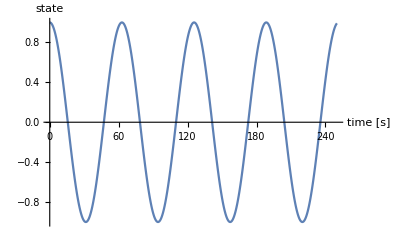

```mathematica
ListPlot[input, Joined->True,AxesLabel->{"time [s]","state"}]
```

### Filter the sample input

```mathematica
output = Table[{i h,input[[1,2]]},{i,0,Num}];
output = Table[{i h,0.0},{i,0,Num}];
```

```mathematica
Do[
output[[i,2]] = (output[[i-1,2]](2-hω) + hω(input[[i,2]]+input[[i-1,2]]))/(2+hω);
,{i,2,Num+1}];
```

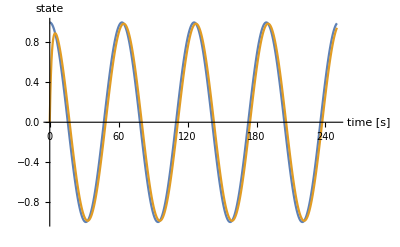

```mathematica
ListPlot[{input,output}, Joined->True,AxesLabel->{"time [s]","state"}]
```

## Particular Filter value check

```mathematica
Num = 1;
input = {{0,1},{0.5,0.9}};
output = input;
```

```mathematica
Do[
output[[i,2]] = (output[[i-1,2]](2-hω) + hω(input[[i,2]]+input[[i-1,2]]))/(2+hω);
,{i,2,Num+1}];
```

```mathematica
output
```

(0 | 1
0.5 | 0.986327)